## beta=40

```mathematica
Delta={2.44,2.54,2.64,2.74,2.84,2.94,3.04,3.14,3.24,3.34,3.44,3.54,3.64};
```

```mathematica
Pd0={4.756849981970399,4.361170897325863,3.972804703953666,3.627451622634275,3.3190415009244663,3.0770558752059527,2.8167468214659293,2.6274674435151533,2.4741780480612277,2.299542606553438,2.166478512571597,2.0566570617694753,1.9493354560418044};
```

```mathematica
(*Vd0={0.408104321 ,0.433944186 ,0.473300845 ,0.510122888 ,0.542222985 ,0.579894727 ,0.608580043 ,0.642279809 ,0.655360925 ,0.681592261 ,0.702933849 ,0.706466824 ,0.723092761};
ldapprox={0.895133817 ,0.909423925 ,0.932113412 ,0.939553303 ,0.946751922 ,0.973793335 ,0.969905339 ,0.962600979 ,0.968499183 ,0.945494341 ,0.957756955 ,0.930862384 ,0.935618726};*)
```

```mathematica
ld={0.7761479095562083,0.8002166852758327,0.829871778922031,0.8491569998530102,0.864491686200576,0.8868210688282607,0.8965838904888813,0.8949891643746429,0.8992432856803027,0.8950969040911091,0.8991701892212216,0.8906075053049668,0.8882218185993381};
```

```mathematica
Pd0vsdelta=Table[{Delta[[i]],Pd0[[i]]},{i,1,13}];
Vd0vsdelta=Table[{Delta[[i]],ld[[i]]/Pd0[[i]]},{i,1,13}];
(*Pd0renormvsdelta=Table[{Delta[[i]],Pd0renorm[[i]]},{i,1,13}];
Vd0renormvsdelta=Table[{Delta[[i]],Vd0renorm[[i]]},{i,1,13}];ldapproxvsdelta=Table[{Delta[[i]],ldapprox[[i]]},{i,1,13}];*)
```

```mathematica
a={Arrowheads[Medium],Arrow[{{2.57,4},{2.37,4}}]};
```

```mathematica
Pd00=ListPlot[{Pd0vsdelta},Frame->True,PlotStyle->{RGBColor[0.368417, 0.506779, 0.709798]},AspectRatio->0.7,BaseStyle->{FontSize->14,FontFamily->"times New Roman"},PlotLegends->Placed[LineLegend[{"P_d0","V_d"},LabelStyle->{13},LegendLayout->{"Row",1}],{0.35,0.92}],FrameLabel->{"Δ (eV)",None},PlotMarkers->{Automatic,10},Joined->True,PlotRangePadding->0,ImagePadding->40,PlotRange->{{2.33,3.73},{1.6,5.3}},FrameTicks->{{All,None},{All,None}}];
```

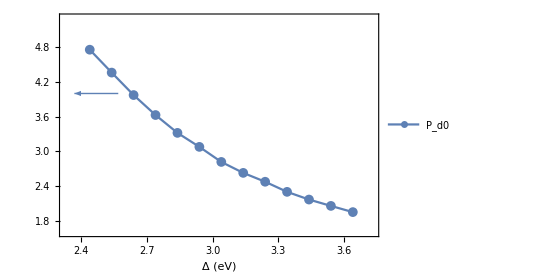

```mathematica
Pd0=Show[Pd00,Graphics[{Thick,RGBColor[0.368417, 0.506779, 0.709798],a}]]
```

```mathematica
b={Arrowheads[Medium],Arrow[{{3.45,0.39},{3.65,0.39}}]};
```

```mathematica
Vd00=ListPlot[{Vd0vsdelta},Frame->True,PlotStyle->{RGBColor[0.880722, 0.611041, 0.142051]},AspectRatio->0.7,BaseStyle->{FontSize->14,FontFamily->"times New Roman"},PlotLegends->Placed[LineLegend[{"V_d"},LabelStyle->{13},LegendLayout->{"Row",1}],{0.55,0.92}],FrameLabel->{"Δ (eV)",None},PlotMarkers->{Automatic,10},Joined->True,PlotRangePadding->0,ImagePadding->40,PlotRange->{{2.33,3.73},{0.13,0.53}},FrameTicks->{{None,All},{All,None}}];
```

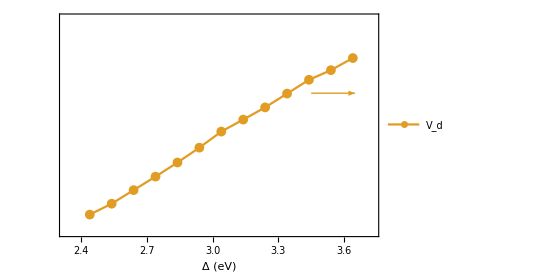

```mathematica
Vd0=Show[Vd00,Graphics[{Thick,RGBColor[0.880722, 0.611041, 0.142051],b}]]
```

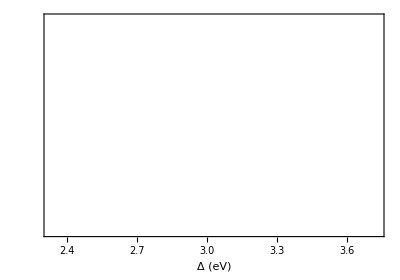

```mathematica
Vd02=ListPlot[{Vd0vsdelta},Frame->True,PlotStyle->{White},AspectRatio->0.7,BaseStyle->{FontSize->14,FontFamily->"times New Roman"},FrameLabel->{"Δ (eV)",None},PlotMarkers->{Automatic,10},Joined->True,PlotRangePadding->0,ImagePadding->40,PlotRange->{{2.33,3.73},{0.36,0.775}},FrameTicks->{{None,Automatic},{All,None}}]
```

```mathematica
Pd0Vd0=Overlay[{Pd0,Vd0}]
```

-Graphics--Graphics-

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
nd={0.6265108871886957,0.6380704469962737,0.6495743035030234,0.6607786201939473,0.6719413757031107,0.6827706077068635,0.6934319557558182,0.7040090887130663,0.7142281163958222,0.7242143947658125,0.7338612400631791,0.7435403016159269,0.7528490299133946};
```

```mathematica
np={0.52388675123141,0.5125062073329938,0.50107450702815,0.4895034133887892,0.47837023702882964,0.4674691237526759,0.4565460501485764,0.4460675095398097,0.4363785709827732,0.4258675076896212,0.4158838825634834,0.4066824895690796,0.39765675501193887};
```

```mathematica
sign={0.88604891,0.82580939,0.8372813,0.79556964,0.76643387,0.72201022,0.70396237,0.67209062,0.62814697,0.57837137,0.57405141,0.5625315,0.48150815};
```

```mathematica
ndvsdelta=Table[{Delta[[i]],nd[[i]]},{i,1,13}];npvsdelta=Table[{Delta[[i]],np[[i]]},{i,1,13}];signvsdelta=Table[{Delta[[i]],sign[[i]]},{i,1,13}];
```

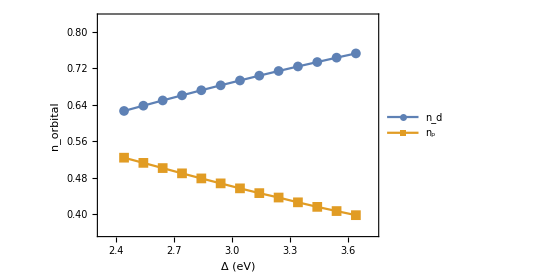

```mathematica
norbitalvsdelta=ListPlot[{ndvsdelta,npvsdelta},AspectRatio->0.7,Frame->True,BaseStyle->{FontSize->14,FontFamily->"times New Roman"},PlotLegends->Placed[LineLegend[{"n_d","n_p"},LabelStyle->{13},LegendLayout->{"Row",1}],{0.35,0.92}],FrameLabel->{"Δ (eV)","n_orbital"},PlotMarkers->{Automatic,10},Joined->True,PlotRangePadding->0,ImagePadding->40,PlotRange->{{2.33,3.73},{0.36,0.83}}]
```

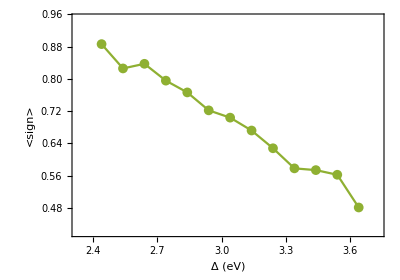

```mathematica
signvsdelta=ListPlot[{signvsdelta},AspectRatio->0.7,Frame->True,PlotStyle->{RGBColor[0.560181, 0.691569, 0.194885]},BaseStyle->{FontSize->14,FontFamily->"times New Roman"},FrameLabel->{"Δ (eV)","<sign>"},PlotMarkers->{Automatic,10},Joined->True,PlotRangePadding->0,ImagePadding->40,PlotRange->{{2.33,3.73},{0.42,0.95}}]
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/norbitalvsdelta.pdf",norbitalvsdelta,"PDF"];
```

```mathematica
Export["/Users/cosdis/Desktop/threeband_project/MS_pairing_correlation/signvsdelta.pdf",signvsdelta,"PDF"];
```